```mathematica
SetDirectory["C:\\Users\\al-ba\\Desktop\\Лабы вычи\\3 лаба\\Lab_3\\Lab_3\\"];
```

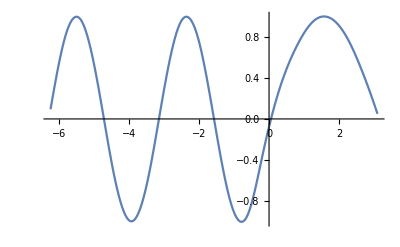

```mathematica
Func=Import["Func.txt","Table"][[2;;]];
LgRavn=Import["LagrangeRavnomer.txt","Table"][[2;;]];
LgCheb=Import["LagrangeChebyshev.txt","Table"][[2;;]];
SpRavn=Import["SplineRavnomer.txt","Table"][[2;;]];
SpCheb=Import["SplineChebyshev.txt","Table"][[2;;]];
a=ListLinePlot[SpRavn, PlotRange->All];
b=ListLinePlot[Func, PlotStyle->Red,PlotRange->All];
Show[a]
```

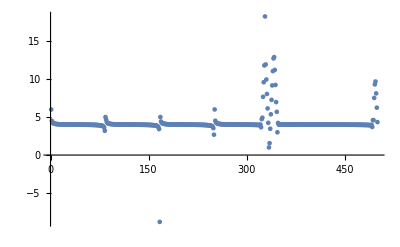

```mathematica
H=Import["SplineRavn_h.txt","List"];
H2=Import["SplineRavn_0.5h.txt","List"];
ListPlot[Log[2,H/H2],PlotRange->Full]
```